```mathematica
(*Зададим параметр λ*)
λ=1/2;
(*Зададим ядро уравнения*)
K[s_,t_]=t*s;
(*Зададим отрезок интегрирования*)
a=0;
b=1;
(*Проверим, что отображение, задаваемое правйо частью уравнения является сжимающим*)
(*Найдем наибольшее значение ядра на квадрате [a;b]x[a;b]*)
M=Maximize[{K[s,t],a≤t≤b,a≤s≤b},{s,t}];
If[λ<1/((b-a)*M[[1]]),
Print["Отображение, задаваемое правой частью интегрального уравнения является сжимающим"],
Print["Думай"]
]
```

Отображение, задаваемое правой частью интегрального уравнения является сжимающим

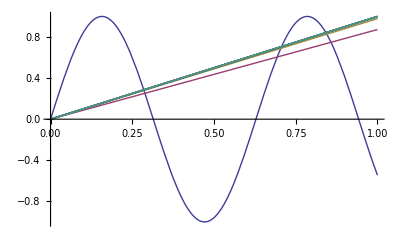

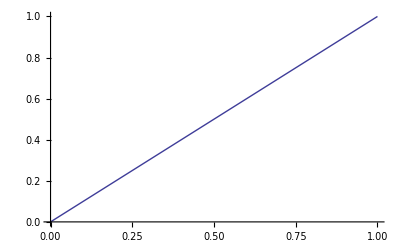

```mathematica
(*Зададим свободный член уравнения*)
f[t_]=5/6*t;
(*Зададим точность вычислений*)
ϵ=10^(-3);
(*Зададим начальное приближение*)
It={Sin[10*t]};
(*Найдем первую итерацию*)
AppendTo[It,f[t]+λ*Integrate[K[s,t]*ReplaceAll[It[[1]],t->s],{s,a,b}]];
(*Найдем расстояние между начальным приближением и первой итерацией в пространстве Чебышева*)
Dist=Maximize[{Abs[It[[2]]-It[[1]]],a≤t≤b},t];
(*Зададим константу сжатия*)
α=Abs[λ]*M[[1]]*(b-a);
(*Найдем количество итераций, используя априорную оценку теоремы Банаха*)
k=Floor[Log[α,ϵ*(1-α)/Dist[[1]]]]+1;
(*Построим последовательность итераций*)
For[i=3,i≤k+1,i++,
AppendTo[It,f[t]+λ*Integrate[K[s,t]*ReplaceAll[It[[i-1]],t->s],{s,a,b}]]
]
(*Построим график последовательности итераций*)
GIt=Plot[It,{t,a,b}]
(*Построим график приближенного решения*)
G=Plot[It[[k+1]],{t,a,b}]
```

Точное решение уравнения имеет вид: t

Найденная функция является решением исходного уравнения

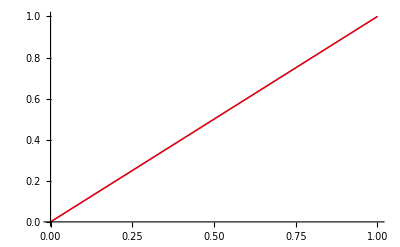

```mathematica
(*Найдем точное решения уравнения*)
P={t};
Q={s};
(*Найдем количество слагаемых в ядре уравнения*)
n=Dimensions[P][[1]];
(*Построим матрицу Фредгольма*)
B=Table[Integrate[Q[[k]]*ReplaceAll[P[[j]],t->s],{s,a,b}],{k,1,n},{j,1,n}];
IM=IdentityMatrix[n];
F=IM-λ*B;
(*Найдем свободные члены системы уравнений*)
A=Table[Integrate[Q[[k]]*f[s],{s,a,b}],{k,1,n}];
(*Найдем коэффициенты решения интегрального уравнения*)
c=Inverse[F].A;
(*Построим решение уравнения*)
x[t_]=f[t]+λ*Sum[c[[k]]*P[[k]],{k,1,n}];
Print["Точное решение уравнения имеет вид: ",x[t]]
(*Выполним проверку*)
If[FullSimplify[x[t]-λ*Integrate[K[s,t]*x[s],{s,a,b}]-f[t]]==0,
Print["Найденная функция является решением исходного уравнения"],
Print["Ищи ошибку"]]
(*Постром график точного и приближенного решения в одной системе координат*)
GS=Plot[x[t],{t,a,b},PlotStyle->Red];
Show[G,GS]
```

```mathematica
Animate[Show[GS,Plot[It[[i]],{t,a,b}]],{i,1,k+1,1},AnimationRunning->False]
```